# Progetto Motori Aeronautici Niccolò D’Ambrosio (2001431), Francesco Daniele (2008421), Elisa Jacopucci (1987922), Matteo Grippo ()

```mathematica
-Graphics-
-Graphics-
```

Real Data (Eurofighter Typhoon , EJ200 Mk.100)

Wing span = 10.95 m
Wing area = 51.2 m^2
AR = 2.34
Length = 15.96 m
Height = 5.28 m
Empty weight = 11000 kg
Gross weight = 16000 kg
MTOW = 23500 Kg
Max payload = 6500 kg
SuperCruise Mach = 1.1
Max Mach / Max speed @ altitude = 2.0 / 2495 km/h
Max Mach / Max speed @ sea level = 1.25 / 1530 km/h
Service ceiling = 16764 m = 55000 ft
Initial climb velocity : 255 m/s (climb at 11.000 m in circa 150 sec)
G limit : +9 / -3 G
Instantaneous turn rate (ITR) : circa 30 gradi/sec
Supported turn rate (STR) : circa 20 gradi/sec
Range = 2900 Km
Seats = 1
TO time < 8 s

Engine Design

Twin-spool TurboFan with Afterburner
3 stages LPC
5 stages HPC
1 stage HPT
1 stages LPT
Inlet diameter = 0.74 m
Fan diameter = 0.74 m
Overall Length = 4 m
Weight = 1037 kg

Engine performance

Thrust @ TO without reheat = 20000 lbf = 90 kN
Thrust @ TO with reheat = 13500 lbf = 60 kN
T/W = 10
Air massflow @ TO =  75/77 kg/s 
Specific thrust @ TO = ? m/s
OPR = 26
BPR = 0.4

Thrust @ CRZ =  lbf = ? N
TSFC @ CRZ = ? Kg / N hr
Estimated(*) air massflow @ CRZ ≃ ? Kg/s 
Estimated(*) Specific thrust @ CRZ ≃ ? m/s

(*) Computed as ρ(h) M_Fan √γRT A_Fan, assuming M_Fan=0.7

## Initialization

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]] (*setta il percorso della directory e le librerie*)
```

C:\Users\nickd\Documents\GitHub\LDG_MOTORI

```mathematica
$ContextPath
```

{ModulesForAircraftEngine`,Units`,ColorDataVisColors`,System`,Global`}

## Constraint Analysis

### Aerodynamics: C_D_0, k_1,k_2 (Polar)

Fighter aircraft C_D_0vs Mach

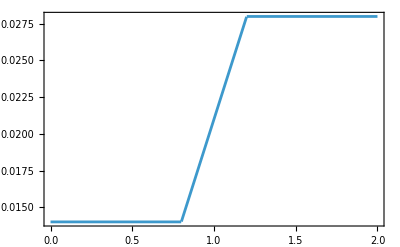

```mathematica
Plot[cd0[False,True,M],{M,0,2},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

### Propulsion: Thrust Lapse α

How (full) thrust varies with altitude and Mach number.

T=α T_SLS

### Low bypass ratio Turbofan

#### Max Power

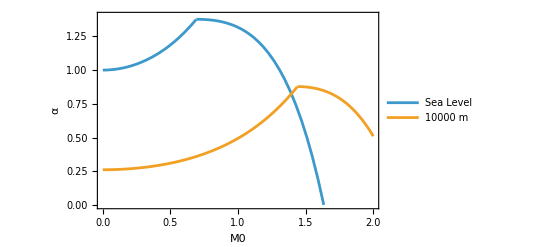

```mathematica
(*TR=1.1*)
Plot[{αLTFmax[0,M0,1.1],αLTFmax[10000,M0,TR]},{M0,0,2},PlotRange->{All,{0,1.4}},AxesLabel->{"M0","α"},PlotLegends->{"Sea Level","10000 m"},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

#### Military Power

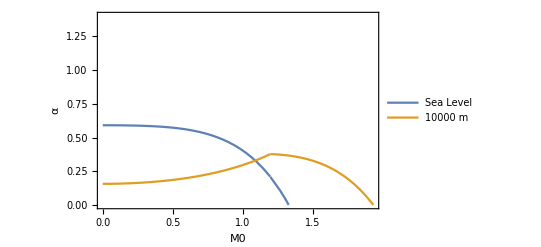

```mathematica
Plot[{αLTFmil[0,M0,TR],αLTFmil[10000,M0,TR]},{M0,0,2},PlotRange->{All,{0,1.4}},AxesLabel->{"M0","α"},PlotLegends->{"Sea Level","10000 m"},Frame->True,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```

### Master Equation

```mathematica
RHS=β/α(q/(β WLG)(K1((n β)/q  WLG)^2+K2((n β)/q  WLG)+CD0+CDR)+Ps/V);
TW==RHS
```

TW==(β (Ps/V+(q (CD0+CDR+(K2 n WLG β)/q+(K1 n^2 WLG^2 β^2)/q^2))/(WLG β)))/α

```mathematica
a=(1.4*287*Tstd[10000])^0.5
```

299.504

### Flight Phases

#### Aircraft Settings

```mathematica
commercial=False;
If[commercial,fighter=False,fighter=True];

AR=2.4;
e=0.8;
(*TR*)
```

#### Mission phases 1-2: Takeoff, no obstacle

#### Mission phases 6-7: Supersonic penetration

dh/dt=0
dV/dt=0
n=1 (L=W)
q assigned
military power

```mathematica
h67=10000;
p067=pstd[h67];
M067=1.6;
β67=0.85;

rule67={Ps->0,
n->1,
q->0.5 γ p067 M067^2,
M0->M067,
h->h67,
β->β67,
α->αLTFmil[h67,M067,TR],
CDR->0,
K1->k1[commercial,fighter,M067,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M067],γ->1.4};
rule67//TableForm
```

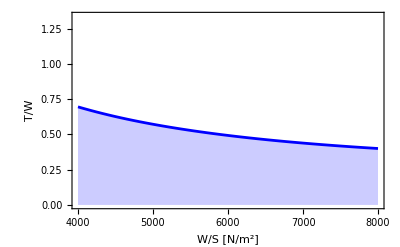

```mathematica
TW67=RHS//.rule67;
plot1=Plot[TW1,{WLG,4000,8000},Filling->Bottom,PlotRange->{All,{0.,1.34}},Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

```mathematica
TW67
```

(94434.7 (0.028+9.27111×10^-11 WLG^2))/WLG

#### Mission phases 7-8: Combat turn 1

#### Mission phases 7-8: Combat turn 2

#### Mission phases 7-8: Horizontal acceleration

#### Mission phases 8-9: Escape dash

dh/dt=0
dV/dt=0
n=1 (L=W)
q assigned
military power

```mathematica
h89=10000;
p089=pstd[h89];
M089=1.4;
β89=0.78; 

rule89={Ps->0,
n->1,
q->0.5 γ p089 M089^2,
M0->M089,
h->h89,
β->β89,
α->αLTFmil[h89,M089,TR],
CDR->0,
K1->k1[commercial,fighter,M089,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M089],γ->1.4};
rule89//TableForm
```

Ps→0
n→1
q→25908.2 γ
M0→1.4
h→10000
β→0.78
α→0.498176
CDR→0
K1→0.252
K2→0
CD0→0.028
γ→1.4

```mathematica
TW89=RHS//.rule89;
plot1=Plot[TW1,{WLG,4000,8000},Filling->Bottom,PlotRange->{All,{0.,1.34}},Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

-Graphics-

```mathematica
TW89
```

(72808.5 (0.028+1.16536×10^-10 WLG^2))/WLG

#### Mission phases 13-14: Landing, no reverse thrust

#### Maximum Mach number @ altitude

#### Maximum Mach number @ sea level

#### Supercruise @ altitude

dh/dt=0
dV/dt=0
n=1 (L=W)
q assigned
military power 
weight after take off, i.e. β = 0.95

```mathematica
hsca=12192;
p0sca=pstd[hsca];
M0sca=1.1;
βsca=0.95; (*Si è osservato che β influisce poco poiché modifica solo il coefficiente di WGL^2 che è comunque dell'ordine di 10^(-10)*)

ruleScrz1={Ps->0,
n->1,
q->0.5 γ p0sca M0sca^2,
M0->M0sca,
TR->1,
h->hsca,
β->βsca,
α->αLTFmil[hsca,M0sca,TR],
CDR->0,
K1->k1[commercial,fighter,M0sca,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0sca],γ->1.4};
rulesca//TableForm
```

Ps→0
n→1
q→11307.5 γ
M0→1.1
h→12192
β→0.95
α→0.236304
CDR→0
K1→0.198
K2→0
CD0→0.0245
γ→1.4

```mathematica
TWsca=RHS//.rulesca;
plotsca=Plot[TW1,{WLG,4000,8000},Filling->Bottom,PlotRange->{All,{0.,1.34}},Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

-Graphics-

```mathematica
TWsca
```

(66992. (0.0245+7.13055×10^-10 WLG^2))/WLG

#### Acceleration @ sea level

dh/dt=0
dV/dt assigned
n=1 (L=W)

```mathematica
g0=9.81;
hAcc=0; (*si osserva che alzando la quota si alza il requisito di T/W*)
p0Acc=pstd[hAcc];
MAcc1=0.3;
MAcc2=1.0;
Mavg=(MAcc2+MAcc1)/2;
VAcc1=MAcc1*Sqrt[γ R Tstd[hAcc]];
VAcc2=MAcc2*Sqrt[γ R Tstd[hAcc]];
ΔT=30;
dV=(VAcc2-VAcc1)/ΔT;
βAcc=0.95;(*si osserva che diminuendo il peso istantaneo si abbassa il requisito di T/W*)

ruleAcc1={Ps->V*dV/g0,
TR->1.0,
n->1,
q->0.5 γ p0Acc Mavg^2,
h->hTurn,
β->βAcc,
α->αTF[hAcc,Mavg,TR],
CDR->0,
K1->k1[commercial,fighter,Mavg,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,Mavg],
M0->Mavg,γ->1.4,R->287};
ruleAcc2={Ps->V*dV/g0,
TR->1.1,
n->1,
q->0.5 γ p0Acc Mavg^2,
h->hTurn,
β->βAcc,
α->αTF[hAcc,Mavg,TR],
CDR->0,
K1->k1[commercial,fighter,Mavg,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,Mavg],
M0->Mavg,γ->1.4,R->287};
```

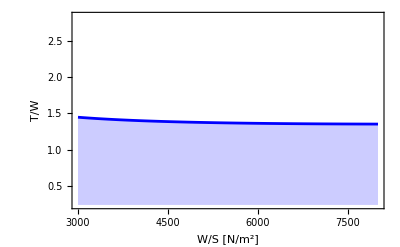

```mathematica
TWAcc1 =RHS//.ruleAcc1;
plotAcc1=Plot[TWAcc1,{WLG,3000,8000},Filling->Bottom,Frame->True,PlotRange->{All,{0.24,2.84}},FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

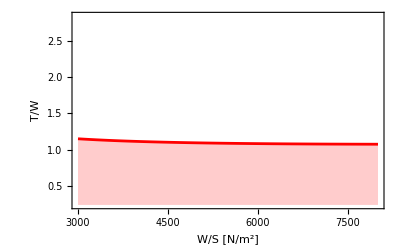

```mathematica
TWAcc2 =RHS//.ruleAcc2;
plotAcc2=Plot[TWAcc2,{WLG,3000,8000},Filling->Bottom,Frame->True,PlotRange->{All,{0.24,2.84}},FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Red},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

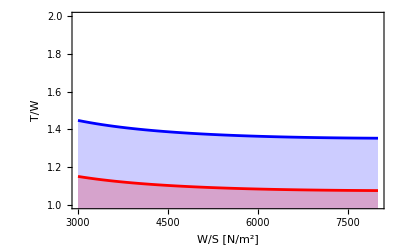

```mathematica
Show[plotAcc1,plotAcc2,PlotRange->{All,{1.0,2}},Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

#### Service ceiling

#### Case 1: Constant Altitude/Speed Cruise (P_s=0)

dh/dt=0
dV/dt=0
n=1 (L=W)
q assigned

```mathematica
hcrz=11000;
p0crz=pstd[hcrz];
M0crz=0.85;
βcrz=0.85;

rule1={Ps->0,
n->1,
q->0.5 γ p0crz M0crz^2,
M0->M0crz,
h->hcrz,
β->βcrz,
α->αLTFmax[hcrz,M0crz,TR],
CDR->0,
K1->k1[commercial,fighter,M0crz,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0crz],γ->1.4};
rule1//TableForm
```

Ps→0
n→1
q→8176.07 γ
M0→0.85
h→11000
β→0.85
α→0.196403
CDR→0
K1→0.18
K2→0
CD0→0.01575
γ→1.4

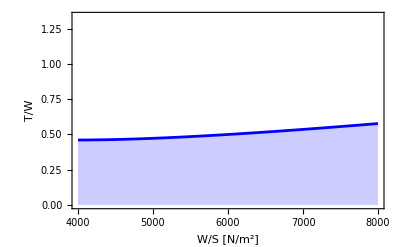

```mathematica
TW1=RHS//.rule1;
plot1=Plot[TW1,{WLG,4000,8000},Filling->Bottom,PlotRange->{All,{0.,1.34}},Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

```mathematica
TW1
```

(0.50575 (cd0[True,False,0.85]+(2.82466 WLG^2 k1[True,False,0.85,2.4,0.8])/pstd[11000]^2+(1.68067 WLG k2[True,False])/pstd[11000]) pstd[11000])/(WLG αTF[11000,0.85,1.1])

#### Case 2: Constant speed climb (P_s=dh/dt)

dV/dt=0
n≈1
h assigned
dh/dt assigned
q assigned

```mathematica
hcas2=11000;
p0cas2=pstd[hcrz];
M0cas2=0.85;
βcas2=0.85;

rule2={Ps->dhdt,
n->1,
q->0.5 γ p0crz M0cas2^2,
M0->M0cas2,
h->hcas2,
β->βcas2,
α->αTF[hcas2,M0cas2,TR],
CDR->0,
K1->k1[commercial,fighter,M0cas2,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0cas2],γ->1.4};
rule2//TableForm
```

Ps→0
n→1
q→8176.07 γ
M0→0.85
h→11000
β→0.85
α→0.196403
CDR→0
K1→0.0597359
K2→-0.004
CD0→0.01915
γ→1.4

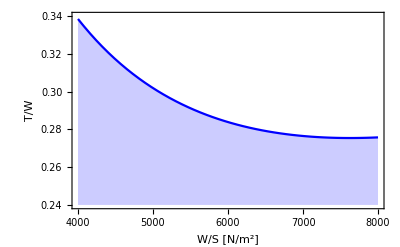

```mathematica
TW1=RHS//.rule2;
plot1=Plot[TW1,{WLG,4000,8000},Filling->Bottom,PlotRange->{All,{0.24,0.34}},Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

#### Case 3: Constant speed/altitude turn (P_s=0)

dh/dt=0
dV/dt=0
n>1
h, q assigned

```mathematica
hTurn=11000;
p0Turn=pstd[hTurn];
βTurn=0.85;
nTurn=1.1;
M0Turn=0.85;

rule3={Ps->0,
n->nTurn,
q->0.5 γ p0Turn M0Turn^2,
h->hTurn,
β->βTurn,
α->αTF[hTurn,M0Turn,TR],
CDR->0,
K1->k1[commercial,fighter,M0Turn,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0Turn],M0->M0Turn,γ->1.4};
rule3//TableForm
```

Ps→0
n→1.1
q→8176.07 γ
h→11000
β→0.85
α→0.196403
CDR→0
K1→0.0597359
K2→-0.004
CD0→0.01915
M0→0.85
γ→1.4

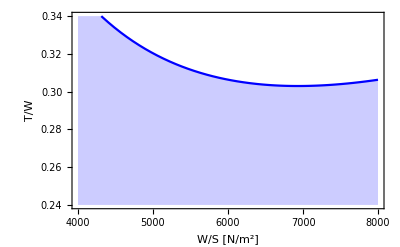

```mathematica
TW3 =RHS//.rule3;
plot3=Plot[TW3,{WLG,4000,8000},Filling->Bottom,PlotRange->{All,{0.24,0.34}},Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

#### Case 4: Horizontal acceleration (P_s=(V/g0)(dV/dt))

dh/dt=0
dV/dt assigned
n=1 (L=W)

```mathematica
g0=9.81;
hAcc=10000;
p0Acc=pstd[hAcc];
MAcc1=0.7;
MAcc2=0.8;
Mavg=(MAcc2+MAcc1)/2;
VAcc1=MAcc1*Sqrt[γ R Tstd[hAcc]];
VAcc2=MAcc2*Sqrt[γ R Tstd[hAcc]];
ΔT=180;
dV=(VAcc2-VAcc1)/ΔT;
βAcc=0.85;

rule4={Ps->V*dV/g0,
n->1,
q->0.5 γ p0Acc Mavg^2,
h->hTurn,
β->βAcc,
α->αTF[hAcc,Mavg,TR],
CDR->0,
K1->k1[commercial,fighter,Mavg,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,Mavg],
M0->Mavg,γ->1.4,R->287};
rule4//TableForm
```

```mathematica
TW4 =RHS//.rule4;
plot4=Plot[TW4,{WLG,4000,8000},Filling->Bottom,Frame->True,PlotRange->{All,{0.24,1.34}},FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

#### Case 5: Takeoff Roll (s_G) when T_SL>>(D+R)

dh/dt=0
s_G assigned
C_L_max assigned 
ρ assigned
V_TO=k_TOV_Stall

```mathematica
hfield=1500;
rule5={kTO->1.2,
sG->2000,
CLmax->2.4,
β->1,
α->αTF[hfield,0,TR],
tr->0};
rule5//TableForm
```

kTO→1.2
sG→2000
CLmax→2.4
β→1
α→0.834505
tr→0

```mathematica
rule5colddensity=ρ->ρstd[hfield,-15.]
rule5hotdensity=ρ->ρstd[hfield,+30]
```

ρ→1.11852

ρ→0.955314

```mathematica
TW5=(β^2/α kTO^2/(sG ρ g0 CLmax)WLG);
```

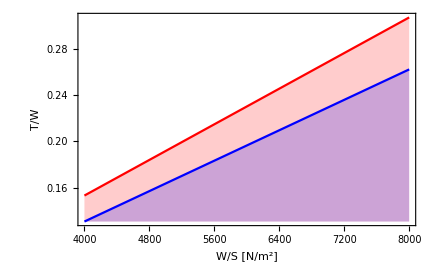

```mathematica
plot5=Plot[{TW5/.rule5hotdensity/.rule5,TW5/.rule5colddensity/.rule5},{WLG,4000,8000},Filling->Bottom,PlotStyle->{Red,Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

#### Case 8: Service Ceiling (P_s=dh/dt)

The maximum altitude at which the aircraft can cruise still having 100ft/min of remaining climb rate. The aircraft has to fly at its maximum efficiency attitude (C_L= √(C_D_0 π AR e)) and full thrust

dV/dt=0
n=1 
C_L assigned -> maximum efficiency C_L
h assigned
dh/dtassigned -> 0.5 m/s = 100 ft/min

```mathematica
ht=0.5;
hCeil=11500;
p0Ceil=pstd[hCeil];
βCeil=0.78;
M0Crit=0.8;
CLe=Sqrt[cd0[commercial,fighter,M0Crit]*Pi AR e];
```

```mathematica
rule8={Ps->ht,
n->1,
q->0.5 γ p0Ceil M0Crit^2,
h->hCeil,
β->βCeil,
α->αTF[hCeil,M0Crit,TR],
CDR->0,
K1->k1[commercial,fighter,M0Crit,AR,e],
K2->k2[commercial,fighter],
CD0->cd0[commercial,fighter,M0Ceil],
V->Sqrt[2 β WLG /( ρstd[hCeil,0] CLe)],
M0Ceil->V/Sqrt[γ R Tstd[hCeil]],γ->1.4,R->287.};
```

```mathematica
TW8 =RHS//.rule8;
```

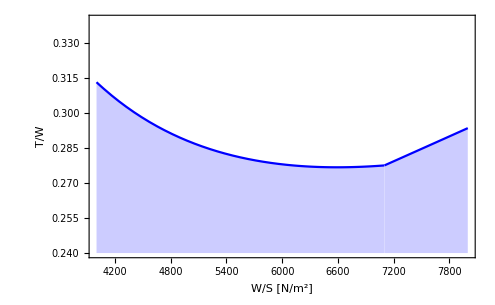

```mathematica
plot8=Plot[TW8,{WLG,4000,8000},Filling->Bottom,Frame->True,PlotRange->{All,{0.24,0.34}},FrameLabel->{"W/S [N/m^2]","T/W"},PlotStyle->{Blue},PlotRange->{All,All},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

### Constraint Diagram

The solution space is the white region over the constraint curves

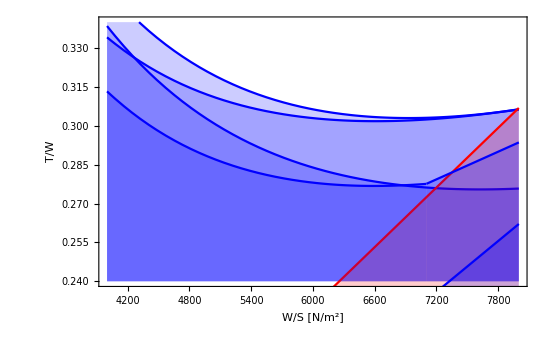

```mathematica
Show[plot1,plot3,plot4,plot5,plot8,Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

```mathematica
TWratio=0.31;
WLG0=6220.;
Print[Style["Aircraft characteristic ratios",20,Bold,Red]];
	Print[TableForm[
	{TWratio,WLG0},
	TableHeadings->{{"Take-Off-Thrust-to-MTOW ratio (T/W) ","Wing loading (W/S) "},None}
	]
];
```

Aircraft characteristic ratios

Take-Off-Thrust-to-MTOW ratio (T/W)  | 0.31
Wing loading (W/S)  | 6220.

### Constant PS contours

V(T-D)/W=(d(V^2/(2 g_0)+h))/dt=dz_e/dt=P_S

where z_e represents the aircraft mechanical energy (kinetic + potential) and is often referred to as “energy height”. P_S is the time rate of change of the energy height and is called weight specific excess power.

Once T/W and W/S are selected, it is possible to compute the weight specific excess power for flight at any chosen β, n, altitude, and velocity. Fighter pilots routinely compare these Ps diagrams for their aircraft with those of their potential adversaries in order to determine where in the flight envelope they enjoy the greatest combat advantage.  CIAOOOOOOOOOOO

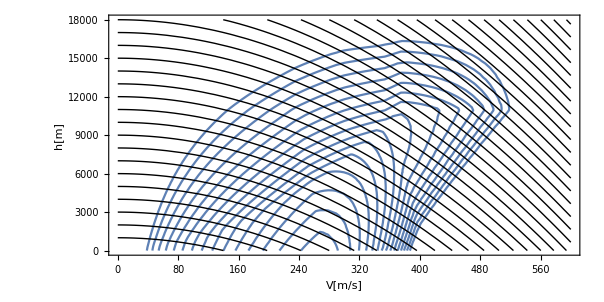

```mathematica
commercial=False;
fighter=True;

Quiet[rulePS={n->1,β->0.97,α->αTJmil[h,M0,1.0],TW->1.,WLG->4000,K1->k1[commercial,fighter,M0,AR,e],K2->k2[commercial,fighter],CD0->cd0[commercial,fighter,M0],q->0.5 ρstd[h,0]V^2,M0->(V/Sqrt[γ R Tstd[h]]),AR->8,e->0.8,γ->1.4,R->287};]


Show[
Table[
ContourPlot[
Evaluate[V(α/β TW-K1 n^2 β/q WLG - K2 n - CD0/(β WLG/q))==cost//.rulePS],
{V,0,600},{h,0,18000},
AspectRatio->0.5,
ContourLabels->None,
FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],
Frame->True,
FrameLabel->{"V[m/s]","h[m]"}],
{cost,0,150,10}],
Table[ContourPlot[h+V^2/(2*9.81)==c1,{V,0,600},{h,0,18000},
ContourStyle->{Black,Thin},
ContourLabels->None],
{c1,0,38000,1000}]
]
```

## Mission Analysis

### TSFC Constants

```mathematica
c1TF=0.45;
c2TF=0.54;
c1LTFmil=0.9;
c2LTFmil=0.3;
c1LTFmax=1.6;
c2LTFmax=0.27;
c1TJmil=1.1;
c2TJmil=0.3;
c1TJmax=1.5;
c2TJmax=0.23;
```

### Best Subsonic Cruise (@ Best Mach = M_crit)

-Graphics-

```mathematica
piCRZ[ΔS_,C1_,C2_,M0_,CD0_,CDR_,K1_,K2_,a_]:=Exp[-(C1/M0+C2)/3600(√(4(CD0+CDR)K1)+K2)ΔS/a]
```

```mathematica
range=4100000; (*~ 2200 nm*)
AR=8;
e=0.8;
Mcrz=0.79;
commercial=True;
fighter=False;
```

```mathematica
ΠCRZ=piCRZ[ΔS,C1,C2,M0,CD0,CDR,K1,K2,a]//.{C1->0.45,C2->0.54,CD0->cd0[commercial,fighter,M0],CDR->0,K1->k1[commercial,fighter,M0,AR,e],K2->k2[commercial,fighter],M0->Mcrz,a->Sqrt[γ R Tstd[hcrz]],ΔS->range,γ->1.4,R->287.}
```

0.771843

### Best Subsonic Cruise Altitude

-Graphics-

#### Initial BCA

```mathematica
βinit=0.95;
WLG0=6220;
```

```mathematica
δinit=(2β)/(γ pstd[0] M0^2)1/(√((CD0+CDR)/K1))WLG0//.{CD0->cd0[commercial,fighter,M0],CDR->0,K1->k1[commercial,fighter,M0,AR,e],M0->0.8,β->βinit,γ->1.4}
```

0.241192

```mathematica
Quiet[BCAinit=h/.Solve[Reduce[δstd[h]==δinit],h][[1]]]
```

10509.5

```mathematica
Solve[delta==(2β)/(γa p0 M0^2)1/(√((CD0+CDR)/K1))WLG,β]
```

{{β→(delta √((CD0+CDR)/K1) M0^2 p0 γa)/(2 WLG)}}

#### 2000 ft steps

Step Climb

```mathematica
steps=Table[(delta √((CD0+CDR)/K1) M0^2 pstd[0] γ)/(2 WLG)//.{CD0->cd0[commercial,fighter,M0],CDR->0,K1->k1[commercial,fighter,M0,AR,e],WLG->WLG0,M0->0.8,delta->δstd[BCAinit+step/3.2808],γ->1.4},{step,2000,8000,2000}]
```

{0.863389,0.783287,0.709311,0.641097}

```mathematica
stepsrange=Quiet[Table[Solve[steps[[j]]==Exp[-(C1/M0+C2)/3600(√(4(CD0+CDR)K1)+K2)ΔS/a]//.{C1->0.45,C2->0.54,CD0->cd0[commercial,fighter,M0],CDR->0,K1->k1[commercial,fighter,M0,AR,e],K2->k2[commercial,fighter],M0->0.8,a->Sqrt[γ R Tstd[hcrz]],γ->1.4,R->287.},ΔS][[1,1]],{j,1,4}]]
```

{ΔS→2.34053×10^6,ΔS→3.89197×10^6,ΔS→5.47269×10^6,ΔS→7.08383×10^6}

```mathematica
ΔS1=ΔS/.stepsrange[[1]]
ΔS2=ΔS/.stepsrange[[2]]
ΔS3=ΔS/.stepsrange[[3]]
ΔS4=ΔS/.stepsrange[[4]]
```

2.34053×10^6

3.89197×10^6

5.47269×10^6

7.08383×10^6

### TO Weight estimation

```mathematica
Γ[WTO_]:=1.02*WTO^(-0.06);
seats=189+6;
baggage=90;
cargo = 3000;
Payload=80*seats+23*baggage+cargo;
Print["Payload = "<>ToString[Payload]]
```

Payload = 20670

```mathematica
WTOguess=200000.;
sol=FindRoot[WTOff==Payload/(1-βinit(1-ΠCRZ)-Γ[WTOff]),{WTOff,WTOguess}]
```

{WTOff→78168.5}

```mathematica
WTO=WTOff/.sol;
Wempty=Γ[WTO]*WTO;
Wfuel=WTO-Payload-Wempty;
Thrust=TWratio*WTO*9.81/2.; (*TWratio is a result of the constraint analysis; assuming twin-engine a/c*)
Print[Style["Aircraft Specifications",20,Bold,Red]];
	Print[TableForm[
	{WTO,Wempty,Payload,Wempty+Payload,Wfuel,Thrust},
	TableHeadings->{{"MTOW [Kg] ","OEW [Kg] ","Payload [Kg] ","MZFW [Kg]","MFW [Kg] ","TO Thrust (one engine) [N]"},None}
	]
];
```

Aircraft Specifications

MTOW [Kg]  | 78168.5
OEW [Kg]  | 40555.5
Payload [Kg]  | 20670
MZFW [Kg] | 61225.5
MFW [Kg]  | 16943.
TO Thrust (one engine) [N] | 118859.

### Payload-Range Diagram

This is a typical performance diagram of civil aviation aircrafts. It depicts the achievable mission range for a given payload.

```mathematica
Payload+(βinit*(1-ΠCRZ))*WTO+Wempty
```

78168.5

```mathematica
m2nm=0.000539957;(*meters to nautical miles*)
```

```mathematica
payloadrange={{0,Wempty+Payload},{range*m2nm,Wempty+Payload}};
towrange={{0,Wempty+Payload},{range*m2nm,Wempty+Payload+Wfuel}};
FuelCapacity = 20700;
PL=Payload;
Fu=Wfuel;
mtow=WTO;
newrange=range;
(*MTOW-limited range*)
While[Fu<FuelCapacity,
PL=PL-50;
Fu=WTO-Wempty-PL;
rangeguess=newrange;
sol=FindRoot[mtow==PL+βinit*(1-piCRZ[rng,c1TF,c2TF,Mcrz,cd0[commercial,fighter,Mcrz],0,k1[commercial,fighter,Mcrz,AR,e],k2[commercial,fighter],Sqrt[1.4*287* Tstd[hcrz]]])*mtow+Wempty,{rng,rangeguess}];
newrange=rng/.sol;
AppendTo[payloadrange,{newrange*m2nm,Wempty+PL}];
AppendTo[towrange,{newrange*m2nm,Wempty+PL+Fu}]
]
(*Fuel-capacity-limited range*)
While[PL>50,
PL=PL-50;
Fu=FuelCapacity;
tow=Wempty+Fu+PL;
rangeguess=newrange;
sol=FindRoot[tow==PL+βinit*(1-piCRZ[rng,c1TF,c2TF,Mcrz,cd0[commercial,fighter,Mcrz],0,k1[commercial,fighter,Mcrz,AR,e],k2[commercial,fighter],Sqrt[1.4*287* Tstd[hcrz]]])*tow+Wempty,{rng,rangeguess}];newrange=rng/.sol;
AppendTo[payloadrange,{newrange*m2nm,Wempty+PL}];
AppendTo[towrange,{newrange*m2nm,Wempty+PL+Fu}]
]
```

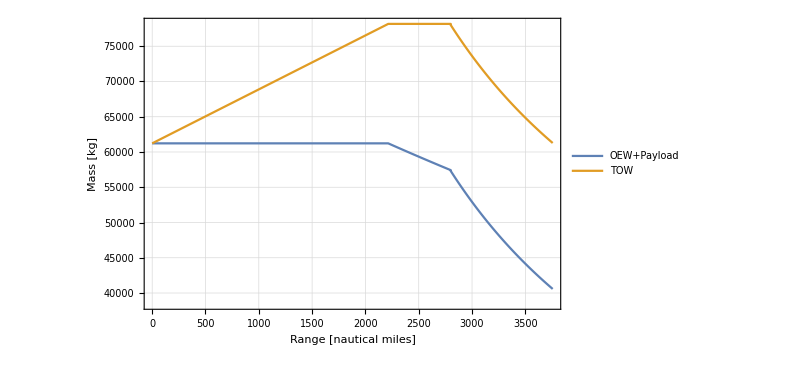

```mathematica
ListLinePlot[{payloadrange,towrange},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],
Frame->True,
FrameLabel->{"Range [nautical miles]","Mass [kg]"},
GridLines->Automatic,
PlotLegends->{"OEW+Payload","TOW"}]
```